#### Dynamics of the rescaled variables (y_i = \chi_i / (M \omega^-1))

```mathematica
ay1=y1*b*r1*(1-om/phi)
ay2=y2*b*r2*(1-om/phi(1+s))
dy1=y1*b*r1*c1*(1+om/phi)/2/M/omi
dy2=y2*b*r2*c2*(1+om/phi)/2/M/omi
```

b (1-om/phi) r1 y1

b r2 (1-(om (1+s))/phi) y2

(b c1 (1+om/phi) r1 y1)/(2 M omi)

(b c2 (1+om/phi) r2 y2)/(2 M omi)

#### Dynamics of the conserved quantity

```mathematica
alp=y2*y1^(-r2/r1);
alpd1=Simplify[D[alp,y1]]
alpdd1=Simplify[D[alp,{y1,2}]]
alpd2=Simplify[D[alp,y2]]
alpdd2=Simplify[D[alp,{y2,2}]]
```

-(r2 y1^(-(r1+r2)/r1) y2)/r1

(r2 (r1+r2) y1^(-2-r2/r1) y2)/r1^2

y1^(-r2/r1)

0

```mathematica
(*Conservation*)
Simplify[alpd1*ay1+alpd2*ay2]/.{s->0}
```

0

```mathematica
aalp=Simplify[Simplify[(alpd1*ay1+alpd2*ay2+alpdd1*dy1+alpdd2*dy2)/.{y1->z,y2->1-z,om->phi}]/.{M->Nt*c2/omi,c1->c2*c,r1->r*r2}]
dalp=Simplify[Simplify[(alpd1^2*dy1+alpd2^2*dy2)/.{y1->z,y2->1-z,om->phi}]/.{M->Nt*c2/omi,c1->c2*c,r1->r*r2}]
```

(b r2 (-1+z) z^(-(1+r)/r) (-c (1+r)+Nt r s z))/(Nt r)

-(b r2 (-1+z) z^(-(2+r)/r) (c-c z+r z))/(Nt r)

```mathematica
aalp=Simplify[Simplify[(alpd1*ay1+alpd2*ay2+alpdd1*dy1+alpdd2*dy2)/.{y1->z,y2->1-z,om->phi}]/.{M->Nt*c2/omi,c1->c2*c,r1->r*r2}]
dalp=Simplify[Simplify[(alpd1^2*dy1+alpd2^2*dy2)/.{y1->z,y2->1-z,om->phi}]/.{M->Nt*c2/omi,c1->c2*c,r1->r*r2}]
```

(b r2 (-1+z) z^(-(1+r)/r) (-c (1+r)+Nt r s z))/(Nt r)

-(b r2 (-1+z) z^(-(2+r)/r) (c-c z+r z))/(Nt r)

#### Dynamics of the dynamics on the slow manifold

```mathematica
alpz=alp/.{y1->z,y2->1-z,r1->r*r2}
alpzd=Simplify[D[alpz,z]]
alpzdd=Simplify[D[alpz,{z,2}]]
```

(1-z) z^(-1/r)

(z^(-(1+r)/r) (-1+z-r z))/r

(z^(-2-1/r) (1+r-z+r z))/r^2

```mathematica
az=Simplify[aalp/alpzd-dalp*alpzdd/alpzd^3]
dz=Simplify[dalp/alpzd^2]
```

-(b r r2 (-1+z) z ((-1+Nt s (-1+z)) (-1+z)+r^2 z (-c+Nt s z)+r (1+c (-2+z)+z+2 Nt s z-2 Nt s z^2)))/(Nt (1+(-1+r) z)^3)

-(b r r2 (-1+z) z (c-c z+r z))/(Nt (1+(-1+r) z)^2)

```mathematica
az=FullSimplify[(az/.{M->Nt*c1/omi,c2->c1/c,r1->r*r2})](*/.{b ->1/r/r2}*)
dz=FullSimplify[(dz/.{M->Nt*c1/omi,c2->c1/c,r1->r*r2})](*/.{b ->1/r/r2}*)
```

-(b r r2 (-1+z) z (1+r-2 c r+c Nt s-(-1+r) (-1+c (r-2 Nt s)) z+c Nt (-1+r)^2 s z^2))/(c Nt (1+(-1+r) z)^3)

-(b r r2 (-1+z) z (c-c z+r z))/(c Nt (1+(-1+r) z)^2)

### Invasion probability

```mathematica
Int=Simplify[Integrate[(az/dz),z]]
logPinv=Simplify[(Int/.z->1)-(Int/.z->0)+Log[c]]
```

(Nt (-1+r) s z)/(-c+r)-Log[1+(-1+r) z]+((-1+c) (c (1+r)-r (1+r+Nt s)) Log[c-c z+r z])/(c-r)^2

(-Nt (c-r) (-1+r) s+(-c^2 r-r (1+Nt s)+c (1+r^2+Nt r s)) Log[c]+(r+c^2 r+Nt r s-c (1+r^2+Nt r s)) Log[r])/(c-r)^2

((1-c r) Log[c/r])/(c-r)+Nt s ((-1+r)/(-c+r)+((-1+c) r Log[c/r])/(-c+r)^2)

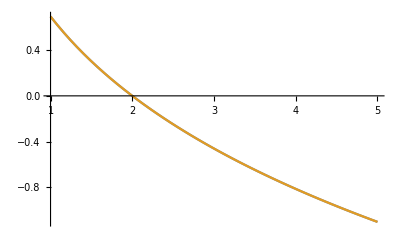

```mathematica
betterLogPinv=Nt s *((r-1)/(r-c)+r*(c-1)/(r-c)^2*Log[c/r]) + (1-r*c)/(c-r)*Log[c/r]
Plot[{betterLogPinv/.{s->2/Nt,c->2},logPinv/.{s->2/Nt,c->2}},{r,1,5}]
```

```mathematica
logPinv/.{s->2/Nt,c->2}
```

-1/2 (5-3 r) x+((2+2 (-1+r)) x)/r-Log[2]